# NG^04 T_09.Метод обратного распространения ошибки

4-апр-2023
Шклярик Вера

## 1. Исходные данные и их стандартизация.

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory";
Map[Dimensions,Test=Import["NG23T09Problem.xlsx"]]
Fig0=Uncompress@Test⟦3,1,1⟧;
Dimensions[Train={{#1,#2},Rationalize@#3}&@@@Test⟦1,2;;⟧]
Dimensions[Test={{#1,#2},{##3}}&@@@Test⟦2,2;;⟧]
```

{{4437,3},{1101,5},{1,1}}

{4436,2}

{1100,2}

```mathematica
Class = Train[[All,2]];
```

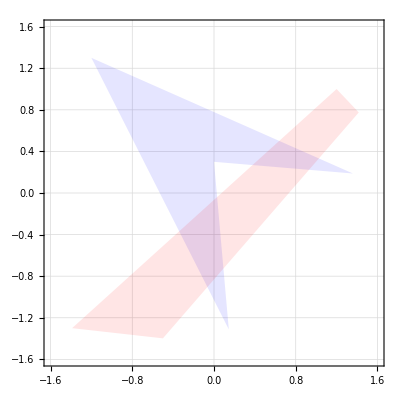

```mathematica
Fig0
```

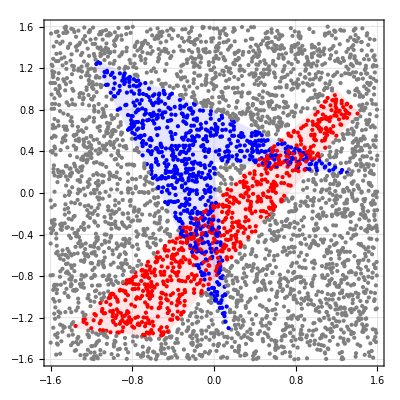

```mathematica
Fig2 = Show[Fig0,Fig1= Graphics[{PointSize@Small,{#2/.{1->Blue,2->Red,3->Gray}, Point@#1}&@@@Train}]]
```

## 2. Полносвязная нейронная сеть прямого распространения.

LReLU(v):=Piecewise[{{α v, v<0}, {v, 0⩽v}}]

SoftMax(V⃗):=(Exp(V⃗))/(∑_n Exp(V_n))

```mathematica
ClearAll[LReLU, SoftMax];
α = 0.01;
LReLU=If[#<0,α #,Min[10.,#]]&
LReLU1= If[#1<0,α,1.]&
SoftMax = Function[#//Exp//#/(Total@#)&//Chop]
SoftMax = Chop@(#/Total[#])&@Map[If[#<-700,0,Min[10,Exp@#]]&,#]&
```

If[#1<0,α #1,Min[10.,#1]]&

If[#1<0,α,1.]&

Chop[(#1/Total[#1]&)[Exp[#1]]]&

(Chop[#1/Total[#1]]&)[(If[#1<-700,0,Min[10,Exp[#1]]]&)/@#1]&

```mathematica
RandomReal[{-1,1},9]
LReLU/@%
Map[LReLU]@%%
Map[LReLU1]@%%%
SoftMax@%%%%
```

{-0.758273,-0.503015,-0.956933,-0.301353,-0.310466,0.227994,0.25031,0.903498,0.495731}

{-0.00758273,-0.00503015,-0.00956933,-0.00301353,-0.00310466,0.227994,0.25031,0.903498,0.495731}

{-0.00758273,-0.00503015,-0.00956933,-0.00301353,-0.00310466,0.227994,0.25031,0.903498,0.495731}

{0.01,0.01,0.01,0.01,0.01,1.,1.,1.,1.}

{0.0488983,0.0631176,0.0400882,0.0772204,0.0765198,0.131106,0.134065,0.257627,0.171357}

```mathematica
Map[LReLU]
```

Map[If[#1<0,α #1,Min[10.,#1]]&]

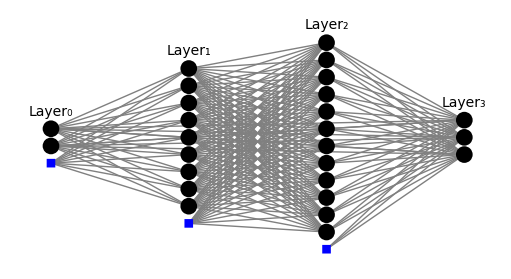
-Graphics-
Рис 2. Трёхслойный персептрон

```mathematica
{2,9,12,3}
Partition[%,2,1]
{#2,#1+1}&@@@%
```

{2,9,12,3}

{{2,9},{9,12},{12,3}}

{{9,3},{12,10},{3,13}}

```mathematica
{2,9,12,3}
Partition[%,2,1]
{#2,#1+1}&@@@%
Map[Dimensions,RandomReal[0.1 {-1,1},#]&/@%]
```

{2,9,12,3}

{{2,9},{9,12},{12,3}}

{{9,3},{12,10},{3,13}}

{{9,3},{12,10},{3,13}}

```mathematica
ClearAll[kmANN];
kmANN["Init",Magnitude_,Signature_]:=Map[Dimensions,kmWeight=Map[RandomReal[{-Magnitude,Magnitude},#]&,{#2,#1+1}&@@@Partition[Signature,2,1]]];
kmANN[X_]:=X//Append[#,1.]&//Dot[kmWeight[[1]],#]&//Map@LReLU//Append[#,1.]&//Dot[kmWeight[[2]],#]&//Map@LReLU//Append[#,1.]&//Dot[kmWeight[[3]],#]&//SoftMax
```

```mathematica
kmANN["Init",3,{2,9,12,3}]
```

{{9,3},{12,10},{3,13}}

```mathematica
RandomChoice@Train[[All,1]]
%//Append[#,1.]&//Dot[kmWeight[[1]],#]&//Map@LReLU//Append[#,1.]&//Dot[kmWeight[[2]],#]&//Map@LReLU//Append[#,1.]&//Dot[kmWeight[[3]],#]&//SoftMax
```

{-1.28126,1.47809}

{0.0440892,3.59545×10^-6,0.955907}

## 3.Визуализация.

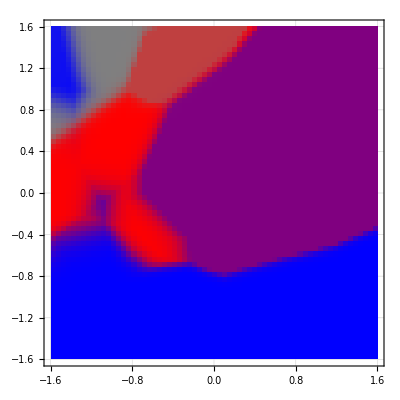

```mathematica
Show[Fig0,Graphics[{Raster[Table[Blend[{Blue,Red,Gray},kmANN@{y,x}]/.RGBColor[c__]:>{c,.3},{x,-1.6,1.6,0.05},{y,-1.6,1.6,0.05}],1.6{{-1,-1},{1,1}}]}]]
```

## 4. Прямой ход обучения.

```mathematica
ClearAll[kmANN];
kmANN["Init",Magnitude_,Signature_]:=Map[Dimensions,kmWeight=Map[RandomReal[{-Magnitude,Magnitude},#]&,{#2,#1+1}&@@@Partition[Signature,2,1]]];
kmANN[X_]:=X//Append[#,1.]&//Dot[kmWeight[[1]],#]&//Map@LReLU//Append[#,1.]&//Dot[kmWeight[[2]],#]&//Map@LReLU//Append[#,1.]&//Dot[kmWeight[[3]],#]&//SoftMax;
kmANN[,X_]:=X//Append[#,1.]&//Sow//Dot[kmWeight[[1]],#]&//Map@LReLU//Append[#,1.]&//Sow//Dot[kmWeight[[2]],#]&//Map@LReLU//Append[#,1.]&//Sow//Dot[kmWeight[[3]],#]&//SoftMax//Sow;
```

```mathematica
RandomChoice@Train[[All,1]]
Reap@kmANN@%
Reap@kmANN[,%%]
Map[Length,%[[2,1]]]
```

{0.700307,-0.317097}

{{0.5,0.5,1.19732×10^-7},{}}

{{0.5,0.5,1.19732×10^-7},{{{0.700307,-0.317097,1.},{2.12596,-0.00939061,-0.0167729,-0.0132626,-0.0266249,0.89457,-0.0392818,-0.0176428,1.64762,1.},{2.61368,-0.0493598,1.81375,-0.0089295,-0.105194,-0.0138459,0.825717,-0.0239399,-0.0425212,-0.0494659,-0.0727042,8.0212,1.},{0.5,0.5,1.19732×10^-7}}}}

{3,10,13,3}

## 5. Локальные градиенты.

```mathematica
{X,Class} = RandomChoice@Train
Y = Reap[kmANN[,X]][[2,1]]
Map[Length,Y]
```

{{-0.164221,1.01281},3}

{{-0.164221,1.01281,1.},{4.70706,3.18451,-0.0155403,0.455759,0.634993,-0.0153347,-0.00527099,0.581919,-0.0291983,1.},{6.94775,-0.169769,-0.037864,-0.046317,-0.140826,8.01811,3.36726,-0.0238552,10.,-0.16487,-0.0527224,10.,1.},{0.492449,0.492449,0.0151012}}

{3,10,13,3}

Loss(W):=-∑_n YT_n Ln(Y_n)

```mathematica
ClearAll[kmLoss];
kmLoss[{X_,Class_}]:=-Total@MapThread[If[0<#1,#1 RealExponent@N@#2,0]&,{UnitVector[3,Class],kmANN@X}];
```

```mathematica
δ={,,}
```

{Null,Null,Null}

```mathematica
δ[[-1]]=UnitVector[3,Class]-Y[[-1]]
```

{-0.492449,-0.492449,0.984899}

```mathematica
δ[[-2]]=δ[[-1]].kmWeight[[-1]]
```

{1.92336,-0.544669,-0.774239,-0.730584,2.13743,1.7942,1.75569,-2.08102,-0.613212,-3.92751,-3.64595,-3.52831,-1.7305}

```mathematica
δ[[-3]]=Dot[Most@δ[[-2]],kmWeight[[-2]]]-Map[LReLU1,Y[[-3]]];
Length@%
```

10

```mathematica
ΔW={,,}
Dimensions[ΔW[[1]]=Outer[Times,Most@δ[[1]] ,Y[[1]]]]
Dimensions[ΔW[[2]]=Outer[Times,Most@δ[[2]] ,Y[[2]]]]
Dimensions[ΔW[[3]]=Outer[Times,Most@δ[[3]] ,Y[[3]]]]
Dimensions/@kmWeight
```

{Null,Null,Null}

{9,3}

{12,10}

{2,13}

{{9,3},{12,10},{3,13}}

## 6. Обратный ход обучения.

```mathematica
ClearAll[kmΔWeight];
kmΔWeight[{X_,Class_}]:=Block[{δ={,,},YT = UnitVector[3,Class],Y =Reap[kmANN[,X]][[2,1]]},δ[[-1]]=YT-Y[[-1]];δ[[-2]]=Most[Dot[δ[[-1]],kmWeight[[-1]]] Map[LReLU1,Y[[-2]]]];δ[[-3]]=Most[Dot[δ[[-2]],kmWeight[[-2]]] Map[LReLU1,Y[[-3]]]];MapThread[Outer[Times,##]&,{δ,Most@Y}]]
```

```mathematica
RandomChoice@Train;
kmΔWeight@%
```

{{{-4.72907,-5.76883,-8.37146},{1.29489,1.57959,2.29223},{-0.0292914,-0.0357315,-0.051852},{-3.17381,-3.87162,-5.61832},{0.0675831,0.0824422,0.119636},{-0.0273718,-0.0333898,-0.0484538},{-0.0755362,-0.0921439,-0.133715},{0.0107311,0.0130904,0.0189963},{0.0264349,0.032247,0.0467954}},{{8.18654,2.14461,-0.0381852,0.233031,-0.0160901,-0.00431676,-0.0409524,-0.0284792,-0.016799,1.95285},{-0.0231831,-0.00607322,0.000108135,-0.00065991,0.0000455647,0.0000122245,0.000115971,0.0000806489,0.0000475725,-0.0055302},{-0.0329544,-0.00863299,0.000153712,-0.000938052,0.0000647696,0.0000173769,0.000164851,0.000114641,0.0000676235,-0.0078611},{-0.0310963,-0.00814623,0.000145045,-0.000885161,0.0000611176,0.0000163971,0.000155556,0.000108177,0.0000638107,-0.00741786},{0.0909767,0.0238329,-0.000424351,0.00258966,-0.000178808,-0.000047972,-0.000455102,-0.000316488,-0.000186687,0.021702},{7.63676,2.00058,-0.0356208,0.217381,-0.0150095,-0.00402686,-0.0382022,-0.0265666,-0.0156709,1.82171},{0.0747286,0.0195765,-0.000348563,0.00212716,-0.000146874,-0.0000394044,-0.000373823,-0.000259964,-0.000153346,0.0178261},{-8.85756,-2.32039,0.0413151,-0.252132,0.0174089,0.0046706,0.0443091,0.0308135,0.018176,-2.11292},{-2.61005,-0.68375,0.0121743,-0.0742955,0.00512987,0.00137628,0.0130565,0.0090798,0.00535591,-0.622614},{-0.167169,-0.043793,0.000779743,-0.0047585,0.000328559,0.0000881485,0.000836249,0.000581545,0.000343037,-0.0398773},{-0.155185,-0.0406534,0.000723843,-0.00441736,0.000305005,0.0000818291,0.000776298,0.000539854,0.000318445,-0.0370185},{-15.0178,-3.93418,0.0700488,-0.427483,0.0295164,0.00791889,0.0751251,0.0522436,0.030817,-3.58241}},{{-2.1251,0.0588817,0.0275259,0.0202292,0.0658527,-1.12454,0.00400062,-1.7359,-3.82247,0.0573072,0.0309403,-5.,-0.5},{-2.1251,0.0588817,0.0275259,0.0202292,0.0658527,-1.12454,0.00400062,-1.7359,-3.82247,0.0573072,0.0309403,-5.,-0.5},{4.25021,-0.117763,-0.0550518,-0.0404584,-0.131705,2.24909,-0.00800124,3.47181,7.64494,-0.114614,-0.0618807,10.,1.}}}

## 7. Эпоха обучения.

```mathematica
iTrain=Range@Length@Train;T$C = UpTo@Floor[0.8 Length@Train];
ClearAll[kmTrain];
kmTrain[miniBatch_,η_]:=Block[{iTeach,iCheck},{iTeach,iCheck}=Partition[RandomSample@iTrain,T$C];Do[AddTo[kmWeight,η Total[kmΔWeight/@Train[[batch]]]],{batch,Partition[iTeach,miniBatch]}];Total[kmLoss/@Train[[iCheck]]]]
```

```mathematica
Total[kmΔWeight/@Train[[{1,22,44,657}]]];
```

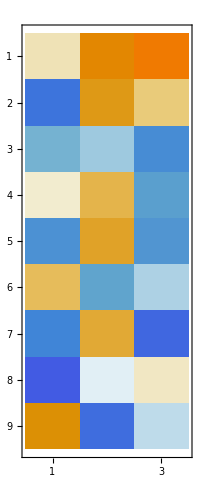
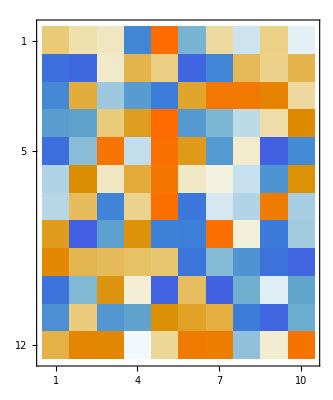
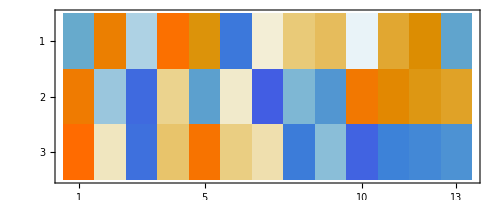

```mathematica
MatrixPlot/@kmWeight
```

## 8. Обучение классификатора.

```mathematica
kmWeight;
```

```mathematica
kmTrain[10,0.02]
```

140.28

```mathematica
CreatePalette@Dynamic[Show[Fig0,Graphics[{Raster[Table[Blend[{Blue,Red,Gray},kmANN@{y,x}]/.RGBColor[c__]:>{c,.3},{x,-1.6,1.6,0.05},{y,-1.6,1.6,0.05}],1.6{{-1,-1},{1,1}}]}],PlotLabel->StringForm["Эпоха = ``, η = ``, Потери = ``",kmEpoch,η,L],ImageSize->300],TrackedSymbols:>{kmEpoch}]
```

```mathematica
kmEpoch = -1; miniBatchSize = 10; η=1.01 0.02;
kmANN["Init",1,{2,9,12,3}]
```

{{9,3},{12,10},{3,13}}

```mathematica
Stop = False;
PrintTemporary[Button["Stop",Stop = True,Method->"Preemptive"]];
Until[Stop,kmEpoch++;L = kmTrain[miniBatchSize,η*=.99]]
```

Обучение завершено на 94-й эпохе, потери колебались в пределах 45-55.

-Graphics-

## 9. Качество обучения.

```mathematica
lenTest = Length@Test
```

1100

```mathematica
Test[[All,2]];
```

```mathematica
RealExponent@Norm[{0.51,0.49,0}-{1.,0,0}]
```

-0.159289

```mathematica
fls = Table[RealExponent@Norm[kmANN@Test[[n,1]]-Test[[n,2]]]<-.5, {n,1,lenTest}];
Errors = Count[fls,False]
```

67

Процент неточно (мы считали ошибкой, если классификатор не полностью “уверен” в правильном ответе) классифицированных точек:

```mathematica
PercentForm[N@(Errors/lenTest)]
```

6.091%

```mathematica
Position[#,Max@#][[1,1]]&/@(kmANN/@Test[[All,1]]);
```

```mathematica
{PointSize@Small,{Position[kmANN@#,Max@kmANN@#][[1,1]]/.{1->Blue,2->Red,3->Gray}, Point@#}&/@Test[[All,1]]}
```

Построим также график, содержащий окрашенные точки как результат работы классификатора.

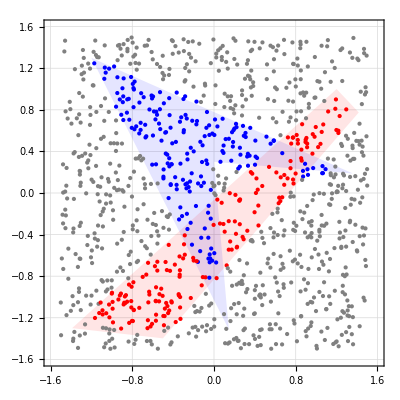

```mathematica
Fig4 = Show[Fig0,Fig3= Graphics[{PointSize@Medium,{Position[kmANN@#,Max@kmANN@#][[1,1]]/.{1->Blue,2->Red,3->Gray}, Point@#}&/@Test[[All,1]]}]]
```